## Spectra Plots

```mathematica
ContextRemove["UWTools`"]
```

```mathematica
<<UWTools`
<<ChemTools`Wavefunctions`
<<ChemTools`Spectroscopy`
<<ChemTools`DataStructures`
WavefunctionsObject;
GridFunctionObject;
CoordinateGridObject;
```

```mathematica
h5Dir=FileNameJoin@{$UWDirectory,"Research", "H5+" };
```

## Notes

#### Notes for the morning since it’s 4:30 AM

Things look somewhat off, seemingly because of the new potential I calculated. So that it’d be done before too long I actually went somewhat *less* refined than the scan I had before, but over a larger range.

Since stuff went pear-shaped or whatever I’m running a new scan over the same larger range, but more refined. I’m including an interpolation to expand things, too. Hopefully these factors get rid of the shift in the frequencies.

In terms of *where* these new shifts are coming from it is essentially 100% the averaged potential energy surface. For the equilibrium H2 position in the shared proton fundamental frequency is raised by about 20 wavenumbers but the potential from averaging over the outer H2s gives results a difference of 200 wavenumbers. The potentials are qualitatively quite similar, but zooming in on a region we can see the differences:

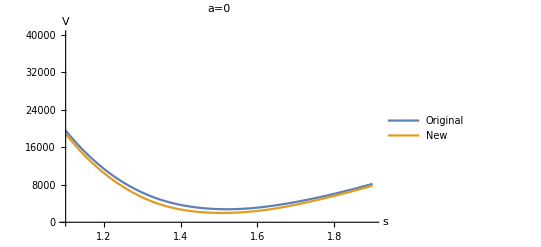

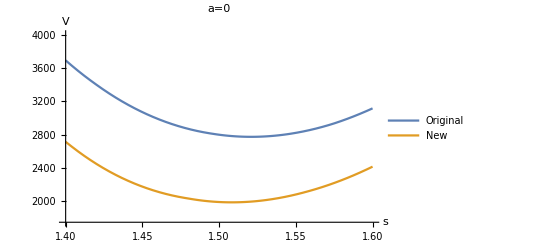

I haven’t looked at the higher excitations, but the working assumption is that the same trend will continue.

## Base Data

### H5

#### Bowtie

```mathematica
h5SpecParts=
Import[FileNameJoin@{h5Dir,"results", "H5HighRes", "Spectra.mx"}];
h5Spec=Join@@h5SpecParts[[;;3]];
```

```mathematica
h5LowResParts=
Import[FileNameJoin@{h5Dir, "results", "H5", "Spectra.mx"}];
h5LowResSpec=Join@@h5LowResParts[[;;3]];
```

```mathematica
h5HighResParts=
Import[FileNameJoin@{h5Dir, "results", "H5ExtraHighRes", "Spectra.mx"}];
h5HighResSpec=Join@@h5HighResParts[[;;3]];
```

#### Parallel

```mathematica
h5ParallelLowResSpecParts=
Import[FileNameJoin@{h5Dir, "results", "H5Parallel", "Spectra.mx"}];
h5ParallelLowResSpec=Join@@h5ParallelLowResSpecParts[[;;3]];
```

```mathematica
h5ParallelSpecParts=
Import[FileNameJoin@{h5Dir, "results", "H5ParallelHighRes", "Spectra.mx"}];
h5ParallelSpec=Join@@h5ParallelSpecParts[[;;3]];
```

### D5

#### Bowtie

```mathematica
d5SpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5HighRes", "Spectra.mx"}];
d5Spec=Join@@d5SpecParts[[;;3]];
```

```mathematica
d5LowResSpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5", "Spectra.mx"}];
d5LowResSpec=Join@@d5SpecParts[[;;3]];
```

#### Parallel

```mathematica
d5ParallelSpecParts=Import[FileNameJoin@{h5Dir, "results", "D5Parallel", "Spectra.mx"}];
d5ParallelSpec=Join@@d5ParallelSpecParts[[;;3]];
```

### Old

##### H5

```mathematica
h5OldSpecParts=
Import[FileNameJoin@{h5Dir,"results", "H5OldOriginal", "$Spectra.mx"}];
h5OldSpec=Join@@h5OldSpecParts[[;;3]];
```

##### D5

```mathematica
d5OldSpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5Old", "$Spectra.mx"}];
d5OldSpec=Join@@d5OldSpecParts[[;;3]];
```

## Specs

### H5

```mathematica
h5LowResParts[[1]]@"Frequencies"
```

#### Lower Res

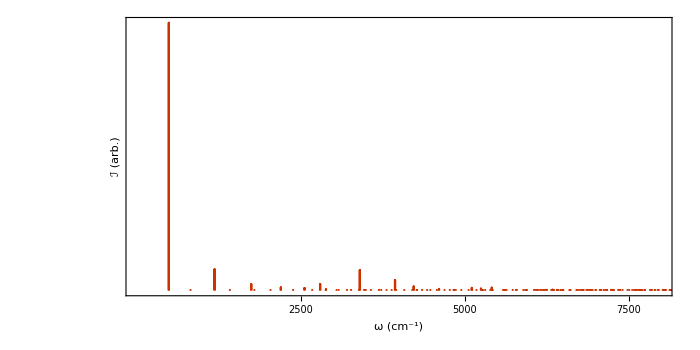

```mathematica
spectrumPlot[h5LowResSpec, PlotRange->{{0, 8000}, {0, 1}}]
```

##### Zoom 1

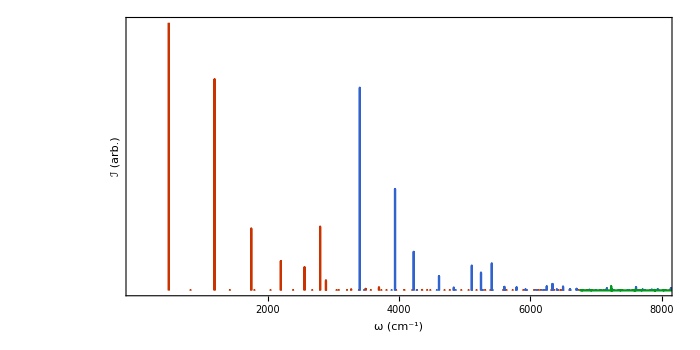

```mathematica
spectrumPlot[h5LowResParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

#### Bowtie

##### Full

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange->{{0, 8000}, {0, 1}}]
```

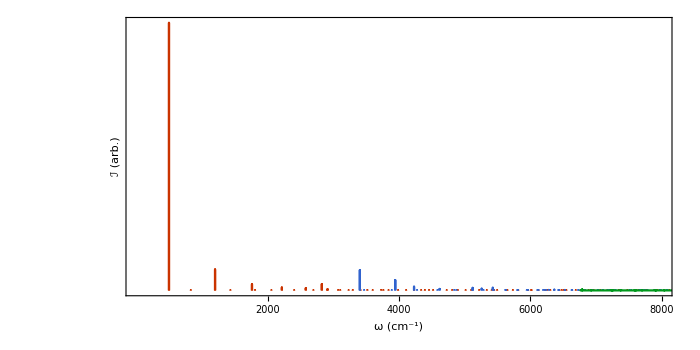

```mathematica
s
```

##### Zoom 1

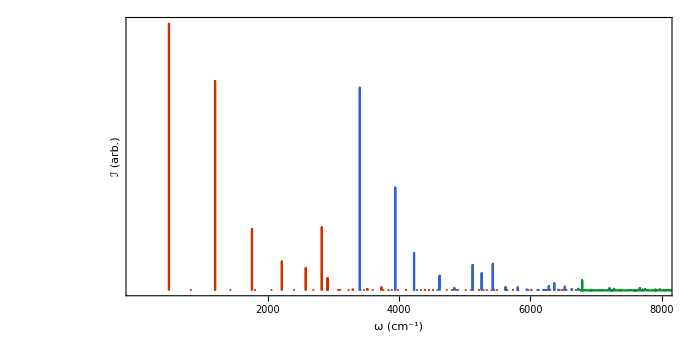

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

##### Zoom 2

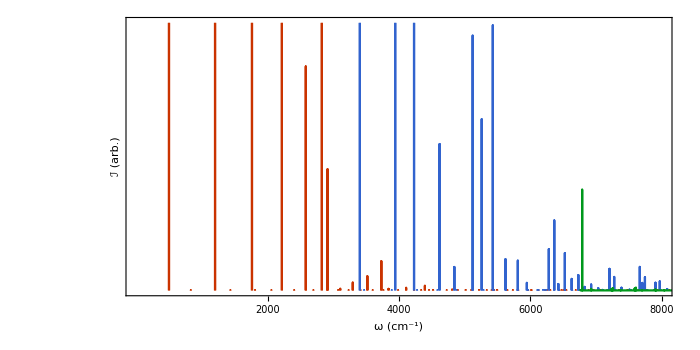

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .01}}]
```

#### Parallel

##### Full

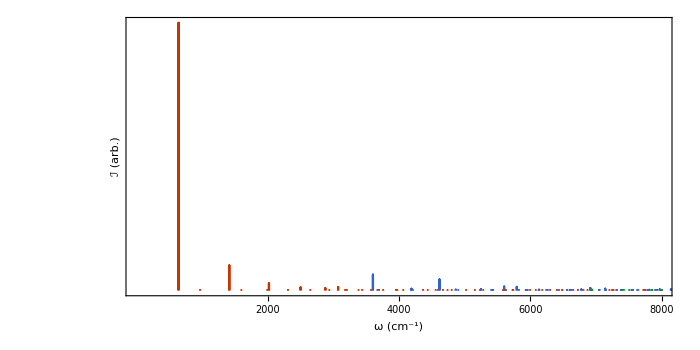

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange->{{0, 8000}, {0, 1}}]
```

##### Zoom 1

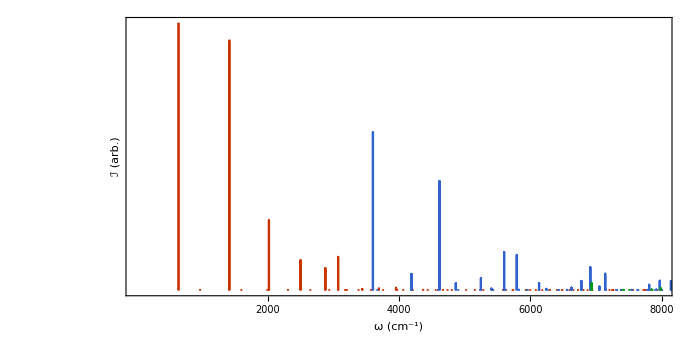

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

##### Zoom 2

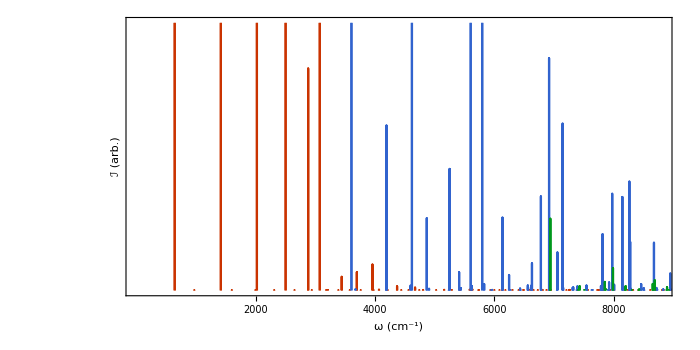

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange-> {{0, 8800}, {0, .01}}]
```

### D5

#### Bowtie

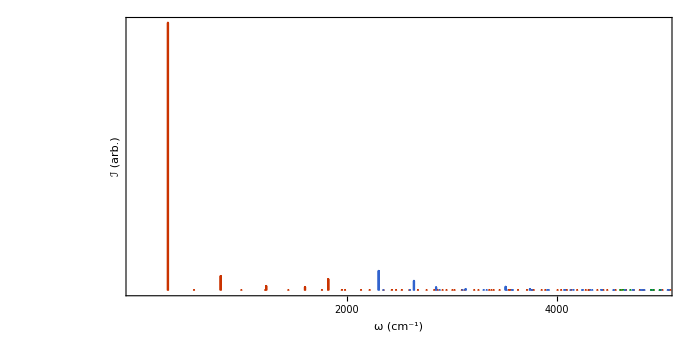

```mathematica
spectrumPlot[d5SpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, 1}}]
```

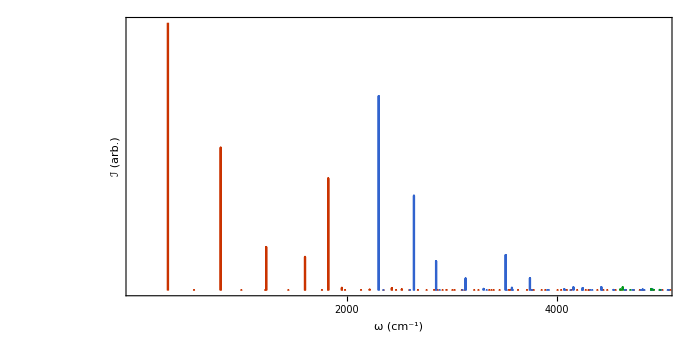

```mathematica
spectrumPlot[d5SpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, .1}}]
```

#### Parallel

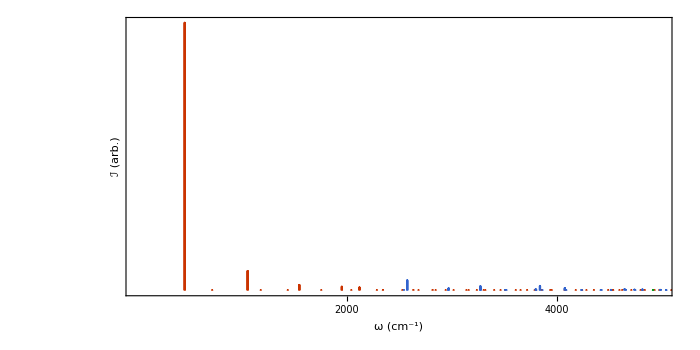

```mathematica
spectrumPlot[d5ParallelSpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, 1}}]
```

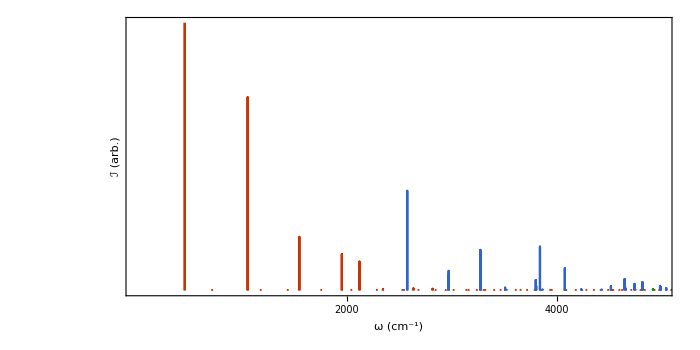

```mathematica
spectrumPlot[d5ParallelSpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, .1}}]
```

### Comparisons of Spectra I Have

#### H Bowtie / Parallel

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### D Bowtie / Parallel

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Old H / New H (something’s weird) / All D

```mathematica
Null
```

Null

### Comparison to Expt

```mathematica
localFig[name_]:=
FileNameJoin@{h5Dir, "figures", name}
```

#### Load Expt. Data

```mathematica
digitData=;
h5Higher=;
spectra=
ChemSpectrum/@
MapThread[
Transpose[{1, #3}*Transpose[MovingAverage[#, #2]]]&,
{
Append[digitData[[{2, 1, 3}]], h5Higher],
{125, 50, 100, 10},
{.08, .1, .01, .01}
}
];
spec1Shift=
940-MaximalBy[spectra[[1]]@"Points", Last][[1, 1]];
spectra[[1]]=
spectra[[1]]@"Shift"[spec1Shift];
spec2Shift=
3520-MaximalBy[spectra[[2]]@"Points", Last][[1, 1]];
spectra[[2]]=
spectra[[2]]@"Shift"[spec2Shift];
spec3Shift=
6684-MaximalBy[spectra[[3]]@"Window"[{5000, All}, {.005, All}]@"Points", Last][[1, 1]];
spectra[[3]]=
spectra[[3]]@"Shift"[spec3Shift];
spec4Shift=
6684-MaximalBy[spectra[[4]]@"Points", Last][[1, 1]];
spectra[[4]]=
spectra[[4]]@"Shift"[spec4Shift];
joinedSpec=Join@@spectra;
```

```mathematica
d5Digit=;
d5Expt=
ChemSpectrum@
Transpose[{1, .1}*Transpose[MovingAverage[d5Digit, 50]]];
```

```mathematica
zhouSpec=ChemSpectrum[…];
```

#### Compare with scales

##### makeCompPlot

```mathematica
makeCompPlot[specs_, spectra_]:=
MapIndexed[
Show[
spectrumPlot[
#, 
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->
Opacity[.5],
AspectRatio->.33,
PlotRange->{All, {-.0150/(10^(#2[[1]]*2/3)), All}}
],
spectrumPlot[
specs
]
]&,
spectra
]//Column[Prepend[#, Show[#, PlotRange->All, FrameTicks->None]]]&
```

##### Orig

```mathematica
properFirstDiff=940-369;
```

```mathematica
neccessaryScale=
properFirstDiff/(
Subtract@@h5OldSpecParts[[1]]["Frequencies"][[{4, 2}]]
);
```

```mathematica
shiftScaledSpecs=
MapThread[
#@"Shift"[#2-#3]@"Scale"[{1, 1}, {#4, #2}]&,
{
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
{369, 3520, 6684},
{
h5OldSpecParts[[1]]["Frequencies"][[2]], 
h5OldSpecParts[[2]]["Frequencies"][[1]],  
h5OldSpecParts[[3]]["Window"[All, {.005, 1}]]["Frequencies"][[1]]
},
neccessaryScale*{1, 1, 1}
}
];
```

```mathematica
plots=makeCompPlot[shiftScaledSpecs,spectra][[1]];
```

```mathematica
MapIndexed[
Export[
localFig["spec_``.pdf"~TemplateApply~#2[[1]]],
Show[#, 
PlotRange->Replace[PlotRange[#], {{a_, b_}, {c_, d_}}:>{{a, a+2800}, {c, d}}]
]
]&,
Rest@plots
];
```

```mathematica
MapIndexed[
Export[
localFig["freq_table_``.pdf"~TemplateApply~#2[[1]]],
figStyleText@
TableForm[
Transpose@
Map[
Take[
PadRight[
Pick[
#["Frequencies"]-#["Frequencies"][[1]],
UnitStep[#@"Intensities"-.0005],
1
],
7,
" "
],
7
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0", "ν=1", "ν=2"}}
]
]&,
Rest@plots
];
```

```mathematica
Iconize[plots, "plots_no_shift"]
```

```mathematica
MapThread[
expFig[localFig["plot_no_shift_``.pdf"~TemplateApply~#2],#]&,
{
,
Range[Length@]
}
]
```

{$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
plots2=
makeCompPlot[
MapThread[
#@"Shift"[#2]@"Scale"[#3]&,
{
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
{0, 200,  350},
{1, 1, 1}
}
],
spectra
][[1]];
```

```mathematica
Iconize[plots2, "plots_shift"]
```

```mathematica
MapThread[
Export["~/Desktop/plot_shift_``.pdf"~TemplateApply~#2,
#
]&,
{
,
Range[Length@]
}
]
```

{~/Desktop/plot_shift_1.pdf,~/Desktop/plot_shift_2.pdf,~/Desktop/plot_shift_3.pdf,~/Desktop/plot_shift_4.pdf,~/Desktop/plot_shift_5.pdf}

```mathematica
makeCompPlot[
h5OldSpecParts[[{1, 2, 3}]],
spectra
]
```

##### H5 Standard

Part::take: Cannot take positions 1 through 3 in h5LowResParts.

MapThread::mptd: Object h5LowResParts⟦1;;3⟧ at position {2, 1} in MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}] has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

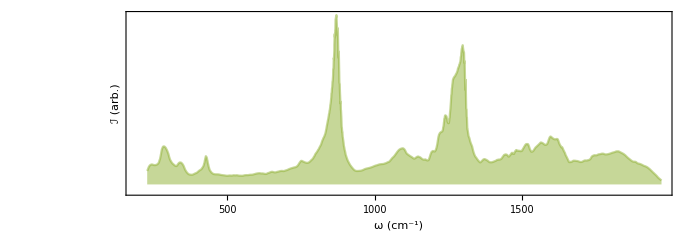
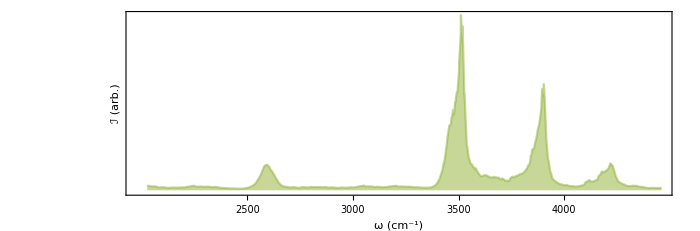
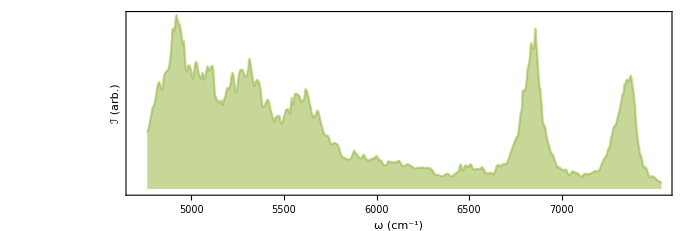
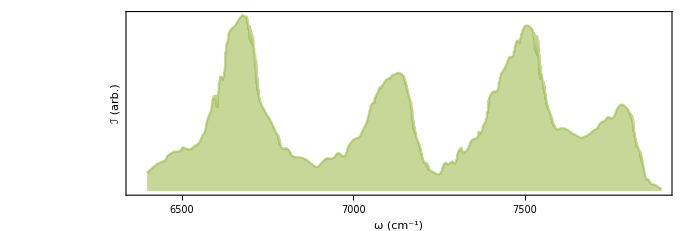
Show[{Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]],Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]],Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]],Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]]},PlotRange→All,FrameTicks→None]
Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]]
Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]]
Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]]
Show[-Graphics-,spectrumPlot[MapThread[#1[Shift[#2][Scale[#3]]]&,{h5LowResParts⟦1;;3⟧,{0,0,0},{1,2,25}}]]]

```mathematica
makeCompPlot[
MapThread[
#@"Shift"[#2]@"Scale"[#3]&,
{
h5LowResParts[[;;3]],
{0, 0,  0},
{1, 2, 25}
}
],
spectra
]
```

##### H5 High Res

```mathematica
basicGrid=
makeCompPlot[
h5SpecParts[[;;3]],
spectra
][[1, 2;;]]//Partition[#,2]&//Grid
```

Part::take: Cannot take positions 1 through 3 in h5SpecParts.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Show[-Graphics-,spectrumPlot[h5SpecParts⟦1;;3⟧]] | Show[-Graphics-,spectrumPlot[h5SpecParts⟦1;;3⟧]]
Show[-Graphics-,spectrumPlot[h5SpecParts⟦1;;3⟧]] | Show[-Graphics-,spectrumPlot[h5SpecParts⟦1;;3⟧]]

```mathematica
expFig["norm_grid",Pane[ basicGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

$Aborted

No Coupling

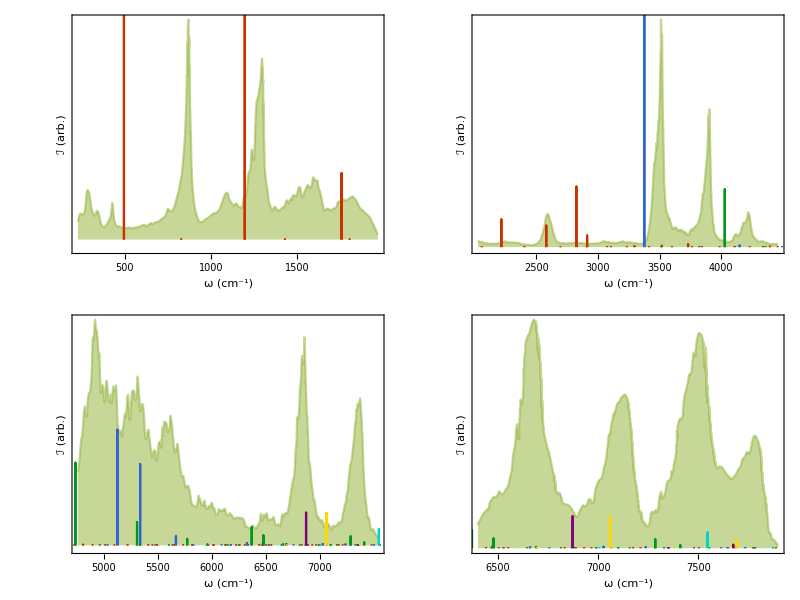

```mathematica
noCupGrid=makeCompPlot[
h5SpecParts[[{1, 5, 6, 7, 8, 9}]],
spectra
][[1, 2;;]]//Partition[#,2]&//Grid
```

```mathematica
expFig["norm_grid_no_cup",Pane[ noCupGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/norm_grid_no_cup.pdf

##### H5Parallel

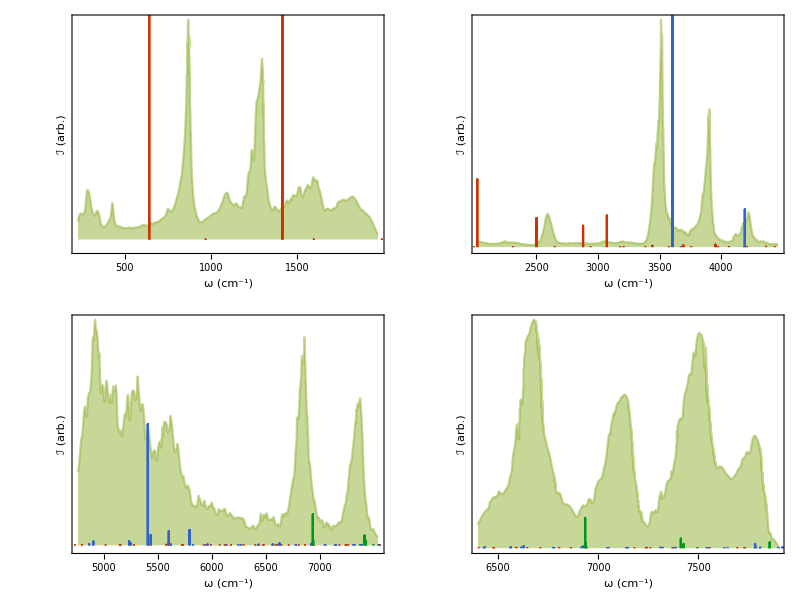

```mathematica
parallelGrid=
Partition[
makeCompPlot[
h5ParallelSpecParts[[;;3]],
spectra
][[1, 2;;]],
2
]//Grid
```

```mathematica
expFig["par_grid", Pane[parallelGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/par_grid.pdf

No Coupling

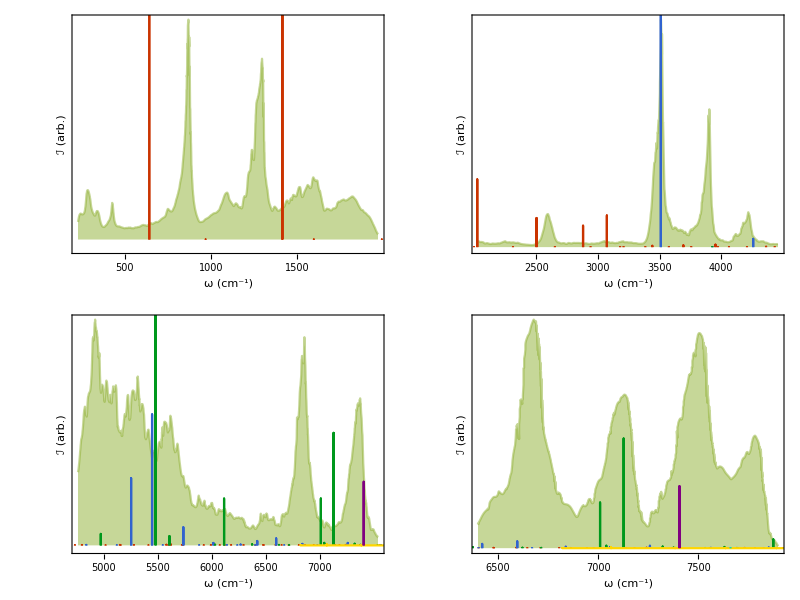

```mathematica
parallelGridNoCup=
Partition[
makeCompPlot[
h5ParallelSpecParts[[{1,5, 6, 7, 8, 9} ]],
spectra
][[1, 2;;]],
2
]//Grid
```

```mathematica
expFig["par_grid_no_cup", Pane[parallelGridNoCup, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/par_grid_no_cup.pdf

##### D5

```mathematica
makeCompPlot[
d5OldSpecParts[[;;3]],
{d5Expt}
]
```

```mathematica
makeCompPlot[
Drop[d5SpecParts, {2, 4}][[;;7]],
{d5Expt}
]
```

```mathematica
expFig["shitty_d5", shittyD5]
```

/Users/Mark/Documents/UW/Research/H5+/figures/shitty_d5.pdf

##### D5Parallel

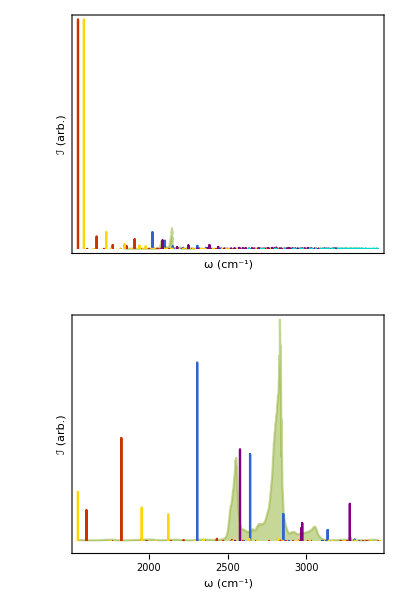

```mathematica
makeCompPlot[
Join[
d5SpecParts[[;;3]],
d5ParallelSpecParts[[;;3]]
],
{d5Expt}
]
```

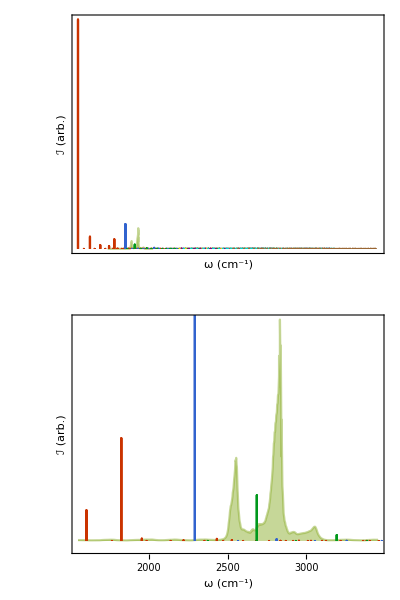

```mathematica
makeCompPlot[
Drop[d5SpecParts, {2, 4}][[;;7]],
{d5Expt}
]
```

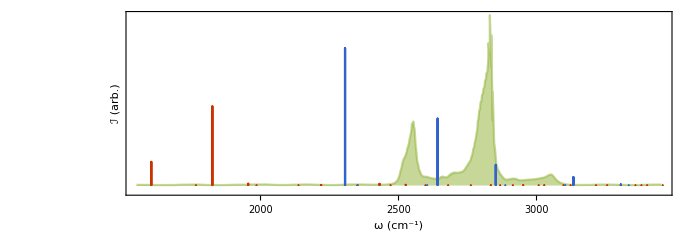
```mathematica
shittyD5=-Graphics-;
```

```mathematica
expFig["shitty_d5", shittyD5]
```

/Users/Mark/Documents/UW/Research/H5+/figures/shitty_d5.pdf

## Wavefunctions

```mathematica
wfns=Import["/Users/Mark/Documents/UW/Research/H5+/results/H5OldOriginal/$Wavefunctions.mx"];
```

```mathematica
wfns[[2]]@"Frequencies"[]
```

{58.6022,439.043,484.132,762.115,803.57,1094.85,1126.97,1344.73,1375.52,1615.88,1627.62,1753.32,1786.67,1906.82,1930.9,2080.57,2081.89,2252.82,2254.01,2401.43,2410.62,2542.1,2555.36,2641.26,2657.97,2685.01,2721.2,2791.32,2800.58,2834.82,2849.16,2919.58,2926.59,3004.21,3016.03,3069.73,3071.59,3155.92,3161.5,3237.36,3240.5,3311.85,3313.99,3397.19,3412.67,3463.56,3471.81,3536.27,3547.74,3580.7,3601.31,3676.3,3693.67,3752.06,3766.09,3878.67,3896.04,3977.79,3987.82,4033.68,4055.39,4093.33,4120.05,4183.39,4198.62,4266.12,4273.79,4319.27,4325.1,4457.47,4468.78,4539.98,4541.6,4572.05,4575.84,4720.34,4726.44,4756.93,4768.05,4860.09,4864.74,4923.04,4927.89,5028.77,5031.06,5065.67,5082.71,5124.57,5136.55,5178.5,5182.25,5253.54,5253.57,5303.58,5317.83,5425.13,5431.12,5442.2,5447.93}

```mathematica
wfns[[2]]@"Frequencies"[]
```

{58.6022,439.043,484.132,762.115,803.57,1094.85,1126.97,1344.73,1375.52,1615.88,1627.62,1753.32,1786.67,1906.82,1930.9,2080.57,2081.89,2252.82,2254.01,2401.43,2410.62,2542.1,2555.36,2641.26,2657.97,2685.01,2721.2,2791.32,2800.58,2834.82,2849.16,2919.58,2926.59,3004.21,3016.03,3069.73,3071.59,3155.92,3161.5,3237.36,3240.5,3311.85,3313.99,3397.19,3412.67,3463.56,3471.81,3536.27,3547.74,3580.7,3601.31,3676.3,3693.67,3752.06,3766.09,3878.67,3896.04,3977.79,3987.82,4033.68,4055.39,4093.33,4120.05,4183.39,4198.62,4266.12,4273.79,4319.27,4325.1,4457.47,4468.78,4539.98,4541.6,4572.05,4575.84,4720.34,4726.44,4756.93,4768.05,4860.09,4864.74,4923.04,4927.89,5028.77,5031.06,5065.67,5082.71,5124.57,5136.55,5178.5,5182.25,5253.54,5253.57,5303.58,5317.83,5425.13,5431.12,5442.2,5447.93}

```mathematica
wfns[[2]][[;;5]]@"Plot"[]
```

#### H5HighRes

```mathematica
h5Wfns=Import["/Users/Mark/Documents/UW/Research/H5+/results/H5HighRes/Wavefunctions.mx"];
```

```mathematica
h5Wfns["OneQuantum"][[;;3]]@"Plot"["PlotMode"->"Density",
AspectRatio->1/2, 
ImageSize->{Automatic, 350}
]
```

```mathematica
h5Wfns["TwoQuanta"][[;;3]]@"Plot"[
BoxRatios->{3, 1, 1}, 
ImageSize->{Automatic, 350}
]
```

### H5Parallel Messed Up

```mathematica
wtf=Import["~/Desktop/r1r2Wavefunctions.mx"];
```

```mathematica
wtf//Keys
```

```mathematica
fuckers=wtf//DeleteCases[$Failed];
```

```mathematica
fuckers//Length
```

3960

```mathematica
fuckers[[800]]@"Grid"//CoordinateBounds
```

{{0.27247,0.976726},{0.27247,0.976726}}

```mathematica
fuckers[[800]][[;;3]]@"Plot"[]
```

```mathematica
Import["/Users/Mark/Documents/UW/Research/H5+/results/D5Old/extrap$39936208.mx"]//ListPlot3D
```